# Midterm 1

Note 1: As in the homework, a partial outline of code is given, but you will need to fill in the blanks. There may also be times when you need to write additional lines of code yourself.

Note 2: If you get to a part where you know exactly what you need to do but don’t know how to make Mathematica do it, please write clearly and explicitly what you would do. We will give you at least partial credit for correct reasoning even if the code doesn’t quite work. (But do your best to get the code to work! All Mathematica techniques you will need for this exam you have already seen in some form in the homework.)

```mathematica
Quit[]
Clear["*"]
```

## Problem 4

Consider a spherical projectile that has a tiny engine strapped to it providing a constant horizontal thrust F_T = 5.0 N. The projectile (including the engine) has a mass of 1.0 kg and a diameter of 0.17 m. In this problem, we will calculate the trajectory of this projectile in the presence of quadratic drag.

A) Calculate the quadratic drag coefficient. Ignore any non-uniformity caused by the tiny engine.

```mathematica
(* given quantities: mass, diameter, gamma, g, engine thrust FT *)
(*mass*)
m=1.0;
(*diameter*)
d=.17;
(*gamma, has units N*s^2/m^4*)
gamma = 0.25;
(*accel due to gravity*)
g=9.81;
(*engine thrust applied horizontaly
* we assume in the positive direction
 *)
FT=5.0;
(* quadratic drag coefficient *)
c = gamma * d^2
```

0.007225

```mathematica
0.00722500000000001
```

Input your answer here (don’t forget units!):
Drag coefficient: c = 0.007225 N*s^2 / m^2

B) Write down the differential equations for the x(t) and y(t) (don’t forget to include the force provided by the engine!). Solve these differential equations numerically for the first 5 seconds given the initial conditions that the projectile is launched from the origin with an initial speed of 32.1 m/s at an angle of 22.45 degrees above the horizontal.

```mathematica
(*differential equations for motion*)
eqx=m*x''[t]==FT - c*Sqrt[x'[t]^2 + y'[t]^2]*x'[t];
eqy=m*y''[t]==-m*g - c*Sqrt[x'[t]^2 + y'[t]^2]*y'[t];

(*initial conditions*)
v0=32.1;
theta=22.45  * Pi/180.0;
vx0=v0*Cos[theta];
vy0=v0*Sin[theta];
(*numerical solve of system*)
sol1=NDSolve[{eqx,eqy,x[0]==0,y[0]==0,x'[0]==vx0,y'[0]==vy0},{x,y},{t,0,5}];
```

C) Plot the trajectory of the projectile and use it to determine the horizontal distance traveled by the projectile to the nearest 0.1 m and the time in the air to the nearest 0.01 s, assuming that the ground is completely flat. Recall that you can adjust the plot viewing window to zoom in. Also, if you want to find the position at a given time, say 1.5 seconds, you can use x[1.5]/.sol1 or y[1.5]/.sol1.

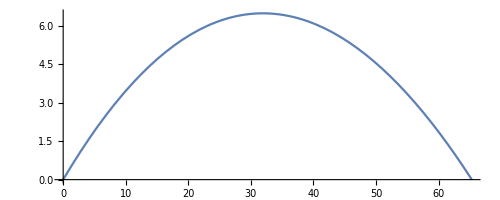

{65.3216}

{-0.00143643}

```mathematica
(*Adjust these tStart and tEnd values to zoom in as necessary*)
tStart=0;
tEnd=2.30195;

ParametricPlot[{x[t],y[t]}/.sol1,{t,tStart,tEnd}]

(* this gives the x and y positions at the time tEnd *)
x[tEnd]/.sol1
y[tEnd]/.sol1
```

Input your answer here:
Horizontal distance traveled: 65.3 meters
Time in the air: 2.30 seconds

D) Calculate the total work done by nonconservative forces (i.e., the engine thrust and the drag) during the flight of the projectile. Note: if you want to find the velocity at a given time, say 1.5 seconds, you can use y’[1.5]/.sol1.

```mathematica
(*The work done by non conservative forces is the change in connected energy and potential energy
 Since the change in potential energy is zero (the start and end have none) all we have to do 
 is calculate the change in kinetic energy which is 0-vfinal.
*)

W = (0.5)*m*(Sqrt[(x'[tEnd]/.sol1)^2 + (y'[tEnd]/.sol1)^2])^2
```

{430.359}

Input your answer here:
Work done by nonconservative forces: -430.359 Joules

E) (Bonus: 1 point) Find another launch angle that will result in the same total horizontal distance traveled for the same initial launch speed.

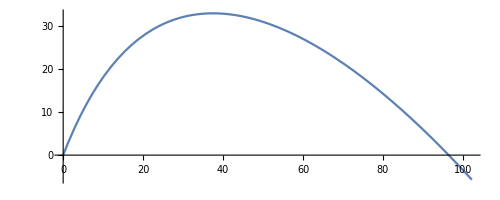

InterpolatingFunction::dmval: Input value {5.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

{102.22}

InterpolatingFunction::dmval: Input value {5.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

{-5.71072}

```mathematica
(*initial conditions*)
v0=32.1;
(* new angle should be 45 degrees plus old theta*)
newtheta=(22.45+45)  * Pi/180.0;
vx0=v0*Cos[newtheta];
vy0=v0*Sin[newtheta];
(*numerical solve of system*)
sol1=NDSolve[{eqx,eqy,x[0]==0,y[0]==0,x'[0]==vx0,y'[0]==vy0},{x,y},{t,0,5}];

(*Adjust these tStart and tEnd values to zoom in as necessary*)
tStart=0;
tEnd=5.5;

ParametricPlot[{x[t],y[t]}/.sol1,{t,tStart,tEnd}]

(* this gives the x and y positions at the time tEnd *)
x[tEnd]/.sol1
y[tEnd]/.sol1
```

Input your answer here:
Alternative launch angle: ????

## Problem 5

```mathematica
Quit[]
```

A small object of mass m = 0.18 kg oscillates on a massless, ideal spring in the presence of linear drag. It is pulled to an initial displacement of 0.17 m and released from rest. Over the course of 20.0 seconds, the system undergoes exactly 23 cycles. You measure the amplitude to be 0.03 m at 20.0 seconds.

A) Without doing any calculations, state whether this system is underdamped or overdamped and explain your reasoning.

Your answer: Underdamped, if it was over damped or critically damped then there would be no oscillations

B) Calculate the oscillation frequency w1, damping constant beta, spring constant k, and natural frequency w0.

```mathematica
(* initial amplitude*)
A0 = 0.17
(*final amplitude*)
Af = 0.03
(*displacement*)
x0 = A0
(*period*)
T = 20/23

m=0.18;
w1 = 23/20.
beta =Log[17/3.]/20
k="????"
w0=Sqrt[k/m]
```

1.15

0.0867301

????

2.35702 √(????)

Input your answer here (don’t forget units!)
w1 = 1.15 s^(-1)
beta = 0.08673 s^(-1)
k = 
w0 =

C) Write down the differential equation corresponding to this system together with the appropriate initial conditions. Solve the equation and use it to find the position of the mass 4.3 seconds after being released.

```mathematica
eq1 ="????"=="????";
sol1 = DSolve[{eq1,x'[0]==0,x[0]==0.17},x[t],t]

(* plot the solution *)
Plot[x[t]/.sol1[[1]],{t,0,20}]

(* extract the position at 4.3 seconds *)
x[t]/.sol1[[1]]/.t->4.3
```

Input your answer here:
Position at 4.3 seconds: ????

D) An external driving force of the form F = (0.35) cos(w*t) is now connected to the spring, where the coefficient 0.35 has units of Newtons. Find the frequency w that yields the largest response of the system (assuming that the driving frequency is the variable but the natural frequency is fixed). Write down and solve the new differential equation, once again assuming that the mass is displaced by 0.17 m and released from rest, with the driving force being turned on at that same instant. Plot the solution for the first 45 seconds.

```mathematica
w = "????"
eq2 ="????"=="????"
sol2 = DSolve[{eq2,x'[0]=="????",x[0]=="????"},x[t],t];

(* plot the solution *)
Plot[x[t]/.sol2[[1]],{t,0,45},PlotRange->Full]
```

Input your answer here (don’t forget units!):
w = ????

E) Considering the same driven system as in part D, calculate the expected amplitude A of the steady-state solution. Then plot the driving force together with the mass’s trajectory from 45 to 50 seconds. Comment on the phase of the mass’s oscillations relative to the driving force. Is this what you expect?

```mathematica
A="????"
Plot[{x[t]/.sol2[[1]],A*Cos[w*t]},{t,45,50},PlotRange->Full,PlotStyle->{Black,Dashed}]
```

Input your answer here (don’t forget units!):
Calculated amplitude: ????
Relative phase: ????